```mathematica
Quit[];
```

```mathematica
d[mphi_,Λ_]:= 8π*Λ^2(125)/mphi^4*(1 - 2 mphi^2/125^2)*(.197*10^-15)*1000(*Converts to mm*);
```

```mathematica
Solve[d[x,1000]==1,x][[4]]
d[.1577,1000]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{x→0.157726}

1.00066

```mathematica
d[2,6*10^5]
```

13.918

```mathematica
masses = Table[i,{i,.1,10,.4}];
```

```mathematica
masses
```

{0.1,0.5,0.9,1.3,1.7,2.1,2.5,2.9,3.3,3.7,4.1,4.5,4.9,5.3,5.7,6.1,6.5,6.9,7.3,7.7,8.1,8.5,8.9,9.3,9.7}

```mathematica
lambdas1mm = Table[Log10[(x/.(Solve[d[i,x]== 1&&x>0,x,Reals]))[[1]]],{i,.1,10,.4}];
lambdaspt1mm =  Table[Log10[(x/.(Solve[d[i,x]== .1&&x>0,x,Reals]))[[1]]],{i,.1,10,.4}];
lambdas5mm =  Table[Log10[(x/.(Solve[d[i,x]== 5&&x>0,x,Reals]))[[1]]],{i,.1,10,.4}];
lambdas10mm =  Table[Log10[(x/.(Solve[d[i,x]== 10&&x>0,x,Reals]))[[1]]],{i,.1,10,.4}];
```

```mathematica
tickspecific = Table[{10^i, Superscript[10,i]},{i,-5,3}];
```

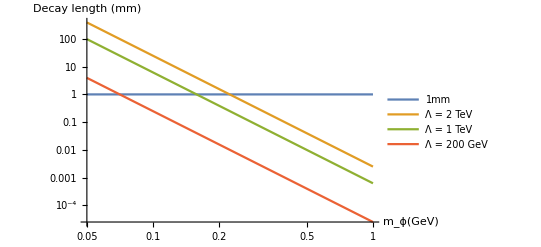

```mathematica
LogLogPlot[{1,d[m,2000],d[m,1000], d[m,200]},{m,.05,1}, PlotLegends->{"1mm","Λ = 2 TeV","Λ = 1 TeV", "Λ = 200 GeV"}, AxesLabel->{Style["m_ϕ(GeV)",16],Style["Decay length (mm)",16]},Ticks->{Automatic,tickspecific},TicksStyle->Directive[FontSize->20]]
```

```mathematica
tick = AbsoluteOptions[ListLogLinearPlot
```

```mathematica
data1mm = Transpose@{Log10[masses],lambdas1mm};
data10mm = Transpose@{Log10[masses],lambdas10mm};
datapt1mm = Transpose@{Log10[masses],lambdaspt1mm};
```

```mathematica
a = ListLinePlot[data1mm, PlotStyle->Blue,PlotLegends->{StringForm["d = `` mm",1],PlotLabel->{Style["Λ vs m_ϕ for given decay length",20]}},AxesLabel->{Style["m_ϕ(GeV)",16],Style["Log_10Λ/GeV",16]},TicksStyle->Directive[FontSize->20]];
b = ListLinePlot[data10mm,PlotStyle->Red,PlotLegends->{StringForm["d = `` mm",10],PlotLabel->{Style["Λ vs m_ϕ for given decay length",20]}},AxesLabel->{Style["m_ϕ(GeV)",16],Style["Log_10Λ/GeV",16]},TicksStyle->Directive[FontSize->20]];
d = ListLinePlot[datapt1mm,PlotStyle->Purple,PlotLegends->{StringForm["d = `` mm",.1]},AxesLabel->{Style["m_ϕ(GeV)",16],Style["Log_10Λ/GeV",16]},TicksStyle->Directive[FontSize->20],PlotLabel->{Style["Λ vs m_ϕ for given decay length",20]}];
```

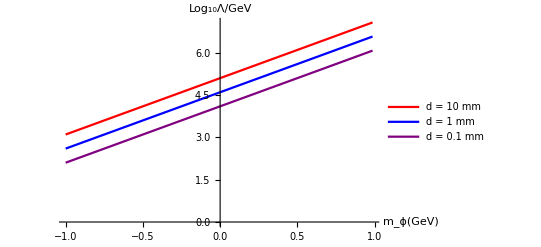

```mathematica
Show[b,a,d]
```